## 1 Initialisation

```mathematica
(*All datasets should be stored in a folder called "DataDir".*)
SetDirectory[FileNameJoin[{NotebookDirectory[],"DataDir"}]];
```

```mathematica
(*This function creates a table for all the fields in the dataset. For numerical data, it summarises "mean","std dev","min","median","max","count of NA","quantile 25%","quantile 50%" and "quantile 75%". For categorical data, it summarises the different categories and "count of NA"*)
statsSummary[dataset_]:=Module[
{keys,keysCat,keysNum,
summary1,summary2,summaryNumDS,summary3,summaryCatDS},

keys=Keys[dataset][[1]]//Normal;
keysCat={};
keysNum={};
If[AllTrue[dataset[All,#]//DeleteMissing,NumericQ],AppendTo[keysNum,#],AppendTo[keysCat,#]]&/@keys;

summary1[key_]:=Query[{Mean/*N,StandardDeviation/*N,Min,Median,Max,Count[_Missing]},key][dataset];
summary2[key_]:=Quantile[dataset[All,key]//DeleteMissing,{1/4,1/2,3/4}];
summaryNumDS=<|#->(AssociationThread[
{"mean","std dev","min","median","max","count#NA","quantile25","quantile50","quantile75"}->
Flatten[Append[summary1[#]//Normal,summary2[#]//Normal]]])|>&/@keysNum//Dataset;

summary3[key_]:=AssociationThread[Normal[If[MissingQ[#],"count#NA",#]&/@Keys[Query[Counts,key][dataset]]]->Normal[Values[Query[Counts,key][dataset]]]]//Dataset;
summaryCatDS=<|#->summary3[#]&/@keysCat//Normal|>//Dataset;

{"rows"->Dimensions[dataset][[1]],
"total#NA"->Length@Select[dataset,MemberQ[#,Missing[]]&],
summaryNumDS,
summaryCatDS}//TableForm
]
```

## 2 Complete dataset 2009 / 2023

### 2.1 Aggregation of the yearly datasets

```mathematica
demand2023=Import["demanddata_2023.csv","Data"];
demand2022=Import["demanddata_2022.csv","Data"];
demand2021=Import["demanddata_2021.csv","Data"];
demand2020=Import["demanddata_2020.csv","Data"];
demand2019=Import["demanddata_2019.csv","Data"];
demand2018=Import["demanddata_2018.csv","Data"];
demand2017=Import["demanddata_2017.csv","Data"];
demand2016=Import["demanddata_2016.csv","Data"];
demand2015=Import["demanddata_2015.csv","Data"];
demand2014=Import["demanddata_2014.csv","Data"];
demand2013=Import["demanddata_2013.csv","Data"];
demand2012=Import["demanddata_2012.csv","Data"];
demand2011=Import["demanddata_2011.csv","Data"];
demand2010=Import["demanddata_2010.csv","Data"];
demand2009=Import["demanddata_2009.csv","Data"];
```

```mathematica
(*The column headings may differ between datasets, here we check if the key columns are presents.*)
{demand2023[[1]], Dimensions[demand2023]}
{demand2022[[1]], Dimensions[demand2022]}
{demand2021[[1]], Dimensions[demand2021]}
{demand2020[[1]], Dimensions[demand2020]}
{demand2019[[1]], Dimensions[demand2019]}
{demand2018[[1]], Dimensions[demand2018]}
{demand2017[[1]], Dimensions[demand2017]}
{demand2016[[1]], Dimensions[demand2016]}
{demand2015[[1]], Dimensions[demand2015]}
{demand2014[[1]], Dimensions[demand2014]}
{demand2013[[1]], Dimensions[demand2013]}
{demand2012[[1]], Dimensions[demand2012]}
{demand2011[[1]], Dimensions[demand2011]}
{demand2010[[1]], Dimensions[demand2010]}
{demand2009[[1]], Dimensions[demand2009]}
```

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,SCOTTISH_TRANSFER,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW,NSL_FLOW,ELECLINK_FLOW,VIKING_FLOW},{17521,21}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW,NSL_FLOW,ELECLINK_FLOW},{17521,19}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW,NSL_FLOW,ELECLINK_FLOW},{17521,19}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW,NSL_FLOW,ELECLINK_FLOW},{17569,19}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW,NSL_FLOW,ELECLINK_FLOW},{17521,19}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW},{17521,17}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW},{17521,17}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW},{17569,17}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW},{17521,17}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW},{17521,17}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW},{17521,17}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW},{17569,17}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW},{17521,17}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW},{17521,17}}

{{SETTLEMENT_DATE,SETTLEMENT_PERIOD,ND,TSD,ENGLAND_WALES_DEMAND,EMBEDDED_WIND_GENERATION,EMBEDDED_WIND_CAPACITY,EMBEDDED_SOLAR_GENERATION,EMBEDDED_SOLAR_CAPACITY,NON_BM_STOR,PUMP_STORAGE_PUMPING,IFA_FLOW,IFA2_FLOW,BRITNED_FLOW,MOYLE_FLOW,EAST_WEST_FLOW,NEMO_FLOW},{17521,17}}

```mathematica
(*We extract the following columns from all the datasets: "SETTLEMENT_DATE","SETTLEMENT_PERIOD","ND","TSD","EMBEDDED_WIND_GENERATION","EMBEDDED_SOLAR_GENERATION".
The date column is reformatted and the day, month and year are extracted from the date in separate columns.*)
demand09to23=Flatten[
#[[2;;,{1,2,3,4,6,8}]]/.{a_,b_,c_,d_,e_,f_}:>{
FromDateString[StringReplace[a,"-"->"/"],TimeZone->None],
DateValue[StringReplace[a,"-"->"/"],"DayName"],
DateObject[StringReplace[a,"-"->"/"],"Month",TimeZone->None],
DateObject[StringReplace[a,"-"->"/"],"Year",TimeZone->None],b,c,d,e,f
}&/@{
demand2009,
demand2010,
demand2011,
demand2012,
demand2013,
demand2014,
demand2015,
demand2016,
demand2017,
demand2018,
demand2019,
demand2020,
demand2021,
demand2022,
demand2023
},1]
```

### 2.2 Check for 0 demand times

No gaps in the ND data.

```mathematica
DeleteDuplicates[Select[demand09to23,#[[6]]==0&][[All,1]]]
```

{}

Gaps in the TSD data follow a pattern, assumed due to system maintenance.

```mathematica
DeleteDuplicates[Select[demand09to23,#[[7]]==0&][[All,1]]]
```

{Sat 29 Aug 2009,Sun 30 Aug 2009,Fri 9 Jul 2010,Sat 10 Jul 2010,Tue 13 Jul 2010,Wed 14 Jul 2010,Tue 29 May 2012,Wed 30 May 2012,Thu 31 May 2012,Fri 1 Jun 2012,Sat 2 Jun 2012,Sun 3 Jun 2012,Mon 4 Jun 2012,Mon 11 Jun 2012,Sun 14 Oct 2012}

Number  of  periods  with  0  demand.

```mathematica
table1=TableForm[Prepend[Tally[Select[demand09to23,#[[7]]==0&][[All,1]]],{"Date","# periods with zero demand"}]]
```

Date | # periods with zero demand
Sat 29 Aug 2009 | 46
Sun 30 Aug 2009 | 2
Fri 9 Jul 2010 | 46
Sat 10 Jul 2010 | 2
Tue 13 Jul 2010 | 46
Wed 14 Jul 2010 | 2
Tue 29 May 2012 | 46
Wed 30 May 2012 | 48
Thu 31 May 2012 | 48
Fri 1 Jun 2012 | 48
Sat 2 Jun 2012 | 48
Sun 3 Jun 2012 | 48
Mon 4 Jun 2012 | 2
Mon 11 Jun 2012 | 46
Sun 14 Oct 2012 | 1

```mathematica
Export["table1.xls",table1]
```

table1.xls

For days with 0 demand for 46 and 48 periods out of 48, we will replace the whole day demand with an average of the first matching working day / non-working day with non-zero demand right before and right after.
For days with 0 demand for just 1 or 2 settlement period, we will replace the demand for these periods with an average of the first periods with non-zero demand right before and right after.

#### 2.2.1 Correction for 29 Aug 2009

The 29 Aug 2009 is a Saturday so we calculate an average demand from the Saturday before the 22 Aug 2009 and the Saturday after 5 Sep 2009.

```mathematica
position1=Position[demand09to23,DateObject[{2009,8,29},"Day"]][[All,1]]
```

{11519,11520,11521,11522,11523,11524,11525,11526,11527,11528,11529,11530,11531,11532,11533,11534,11535,11536,11537,11538,11539,11540,11541,11542,11543,11544,11545,11546,11547,11548,11549,11550,11551,11552,11553,11554,11555,11556,11557,11558,11559,11560,11561,11562,11563,11564,11565,11566}

```mathematica
{demand09to23[[11183,1]],demand09to23[[11902,1]]}
```

{Sat 22 Aug 2009,Sat 5 Sep 2009}

```mathematica
twentyTwoAugust=Table[demand09to23[[n,7]],{n,11183,11230,1}]
```

{26885,26128,25819,25550,24895,24428,24320,24291,24123,24026,23775,23801,24452,25007,25949,27608,29789,31556,33046,33739,34393,34578,34675,34720,34622,34239,33746,33264,32706,32135,31957,31884,32137,32676,33441,33442,33269,32948,32339,31835,32164,33581,33199,32120,30849,29438,28146,27085}

```mathematica
fiveSeptember=Table[demand09to23[[n,7]],{n,11855 ,11902,1}]
```

{27076,26007,25983,25681,25123,24839,24680,24624,24376,24282,24347,24618,25119,25482,26320,27926,30057,31425,32849,33536,33947,34098,34252,34333,34393,33995,33516,32846,32443,32094,31914,31867,32322,33099,33897,34175,34265,34229,34260,34717,34972,34339,33430,32232,30854,29513,28117,26983}

```mathematica
replace1=Thread[Mean[{twentyTwoAugust,fiveSeptember}]]//N
```

{26980.5,26067.5,25901.,25615.5,25009.,24633.5,24500.,24457.5,24249.5,24154.,24061.,24209.5,24785.5,25244.5,26134.5,27767.,29923.,31490.5,32947.5,33637.5,34170.,34338.,34463.5,34526.5,34507.5,34117.,33631.,33055.,32574.5,32114.5,31935.5,31875.5,32229.5,32887.5,33669.,33808.5,33767.,33588.5,33299.5,33276.,33568.,33960.,33314.5,32176.,30851.5,29475.5,28131.5,27034.}

Replacement of the 0 demand periods with the average values

```mathematica
(demand09to23[[position1[[#]],7]]=replace1[[#]])&/@Range[48]
```

{26980.5,26067.5,25901.,25615.5,25009.,24633.5,24500.,24457.5,24249.5,24154.,24061.,24209.5,24785.5,25244.5,26134.5,27767.,29923.,31490.5,32947.5,33637.5,34170.,34338.,34463.5,34526.5,34507.5,34117.,33631.,33055.,32574.5,32114.5,31935.5,31875.5,32229.5,32887.5,33669.,33808.5,33767.,33588.5,33299.5,33276.,33568.,33960.,33314.5,32176.,30851.5,29475.5,28131.5,27034.}

#### 2.2.2 Correction for 30 Aug 2009

```mathematica
Position[demand09to23,DateObject[{2009,8,30},"Day"]]
```

{{11567,1},{11568,1},{11569,1},{11570,1},{11571,1},{11572,1},{11573,1},{11574,1},{11575,1},{11576,1},{11577,1},{11578,1},{11579,1},{11580,1},{11581,1},{11582,1},{11583,1},{11584,1},{11585,1},{11586,1},{11587,1},{11588,1},{11589,1},{11590,1},{11591,1},{11592,1},{11593,1},{11594,1},{11595,1},{11596,1},{11597,1},{11598,1},{11599,1},{11600,1},{11601,1},{11602,1},{11603,1},{11604,1},{11605,1},{11606,1},{11607,1},{11608,1},{11609,1},{11610,1},{11611,1},{11612,1},{11613,1},{11614,1}}

Demand for 30 Aug 2009

```mathematica
Table[demand09to23[[n,7]],{n,11567,11614,1}]
```

{0,0,24340,23950,23643,23315,23309,23293,23102,22990,22985,23041,23023,23266,23199,23958,25678,27111,28768,30024,31200,31918,32412,32892,33194,33161,32582,31995,31646,31318,31269,31391,31584,32152,32653,32810,32784,32639,32649,32633,33566,33133,32452,31223,30022,28722,28307,27551}

Replacement of the first two periods values with the average of the first non-null period before and after

```mathematica
replace2=Mean[{demand09to23[[11566,7]],demand09to23[[11569,7]]}]
```

25687.

```mathematica
demand09to23[[11567,7]]=replace2;
demand09to23[[11568,7]]=replace2;
```

#### 2.2.3 Correction for 9 July 2010

The 9 Jul 2010 is a working day so I calculate an average demand from the working day before the 8 Jul 2010 and the working day after 12 Jul 2010.

```mathematica
position3=Position[demand09to23,DateObject[{2010,7,9},"Day"]][[All,1]]
```

{26591,26592,26593,26594,26595,26596,26597,26598,26599,26600,26601,26602,26603,26604,26605,26606,26607,26608,26609,26610,26611,26612,26613,26614,26615,26616,26617,26618,26619,26620,26621,26622,26623,26624,26625,26626,26627,26628,26629,26630,26631,26632,26633,26634,26635,26636,26637,26638}

```mathematica
eightJuly=Table[demand09to23[[n,7]],{n,26543,26590,1}]
```

{27153,26309,26209,26063,25736,25404,25303,25362,25265,24882,24791,25638,27638,30465,34150,36615,38266,39105,39790,40143,40397,40417,40640,40747,40885,40727,40483,40248,40220,40073,39916,40031,40293,40618,40576,39889,39242,38467,37537,36913,36000,35826,35874,35890,35775,34023,32326,30649}

```mathematica
twelveJuly=Table[demand09to23[[n,7]],{n,26735 ,26782,1}]
```

{26848,26051,25894,25598,25088,24602,24709,24865,24900,24644,24759,25473,27237,29835,33737,36327,38414,39364,39998,40557,40859,40880,41191,41321,41372,41232,41473,41198,40975,40723,40493,40738,41173,41628,41560,40869,39834,38951,38050,37312,36519,35976,35851,35697,34973,33131,31623,30224}

```mathematica
replace3=Thread[Mean[{eightJuly,twelveJuly}]]//N
```

{27000.5,26180.,26051.5,25830.5,25412.,25003.,25006.,25113.5,25082.5,24763.,24775.,25555.5,27437.5,30150.,33943.5,36471.,38340.,39234.5,39894.,40350.,40628.,40648.5,40915.5,41034.,41128.5,40979.5,40978.,40723.,40597.5,40398.,40204.5,40384.5,40733.,41123.,41068.,40379.,39538.,38709.,37793.5,37112.5,36259.5,35901.,35862.5,35793.5,35374.,33577.,31974.5,30436.5}

Replacement of the 0 demand periods with the average values

```mathematica
(demand09to23[[position3[[#]],7]]=replace3[[#]])&/@Range[48]
```

{27000.5,26180.,26051.5,25830.5,25412.,25003.,25006.,25113.5,25082.5,24763.,24775.,25555.5,27437.5,30150.,33943.5,36471.,38340.,39234.5,39894.,40350.,40628.,40648.5,40915.5,41034.,41128.5,40979.5,40978.,40723.,40597.5,40398.,40204.5,40384.5,40733.,41123.,41068.,40379.,39538.,38709.,37793.5,37112.5,36259.5,35901.,35862.5,35793.5,35374.,33577.,31974.5,30436.5}

#### 2.2.4 Correction for 10 Jul 2010

```mathematica
Position[demand09to23,DateObject[{2010,7,10},"Day"]]
```

{{26639,1},{26640,1},{26641,1},{26642,1},{26643,1},{26644,1},{26645,1},{26646,1},{26647,1},{26648,1},{26649,1},{26650,1},{26651,1},{26652,1},{26653,1},{26654,1},{26655,1},{26656,1},{26657,1},{26658,1},{26659,1},{26660,1},{26661,1},{26662,1},{26663,1},{26664,1},{26665,1},{26666,1},{26667,1},{26668,1},{26669,1},{26670,1},{26671,1},{26672,1},{26673,1},{26674,1},{26675,1},{26676,1},{26677,1},{26678,1},{26679,1},{26680,1},{26681,1},{26682,1},{26683,1},{26684,1},{26685,1},{26686,1}}

Demand for 10 July 2010

```mathematica
Table[demand09to23[[n,7]],{n,26639,26686,1}]
```

{0,0,27548,26942,26322,25834,25638,25570,25227,24491,24111,24339,25619,26293,27472,29310,31583,33224,34657,35237,35676,35697,35815,35723,35651,35204,34780,34402,34013,33648,33532,33465,33646,33931,34361,34376,34093,33611,33067,32461,31846,31366,31338,32016,31894,30718,29223,28097}

Replacement of the first two periods values with the average of the first non-null period before and after

```mathematica
replace4=Mean[{demand09to23[[26638,7]],demand09to23[[26641,7]]}]
```

28992.3

```mathematica
demand09to23[[26639,7]]=replace4;
demand09to23[[26640,7]]=replace4;
```

#### 2.2.5 Correction for 13 July 2010

Calculation of average demand for each settlement period for the 12 July 2010 and the 15 July 2010 since the 14 July 2010 also contains 0 demand periods.

```mathematica
position5=Position[demand09to23,DateObject[{2010,7,13},"Day"]][[All,1]]
```

{26783,26784,26785,26786,26787,26788,26789,26790,26791,26792,26793,26794,26795,26796,26797,26798,26799,26800,26801,26802,26803,26804,26805,26806,26807,26808,26809,26810,26811,26812,26813,26814,26815,26816,26817,26818,26819,26820,26821,26822,26823,26824,26825,26826,26827,26828,26829,26830}

```mathematica
{demand09to23[[26848,1]],demand09to23[[28244,1]]}
```

{Wed 14 Jul 2010,Thu 12 Aug 2010}

```mathematica
twelveJuly=Table[demand09to23[[n,7]],{n,26735,26782,1}]
```

{26848,26051,25894,25598,25088,24602,24709,24865,24900,24644,24759,25473,27237,29835,33737,36327,38414,39364,39998,40557,40859,40880,41191,41321,41372,41232,41473,41198,40975,40723,40493,40738,41173,41628,41560,40869,39834,38951,38050,37312,36519,35976,35851,35697,34973,33131,31623,30224}

```mathematica
fifteenJuly=Table[demand09to23[[n,7]],{n,26879 ,26926,1}]
```

{28244,27418,27163,26710,26214,26043,25683,25665,25588,25189,24905,25551,27292,29843,33361,35957,37818,38418,39553,39889,39970,40041,40446,40532,40627,40333,40068,39649,39493,39044,39089,39340,39776,40168,40060,39381,38635,37546,36708,36054,35553,35114,35155,34786,33982,32150,29872,28264}

```mathematica
replace5=Thread[Mean[{twelveJuly,fifteenJuly}]]//N
```

{27546.,26734.5,26528.5,26154.,25651.,25322.5,25196.,25265.,25244.,24916.5,24832.,25512.,27264.5,29839.,33549.,36142.,38116.,38891.,39775.5,40223.,40414.5,40460.5,40818.5,40926.5,40999.5,40782.5,40770.5,40423.5,40234.,39883.5,39791.,40039.,40474.5,40898.,40810.,40125.,39234.5,38248.5,37379.,36683.,36036.,35545.,35503.,35241.5,34477.5,32640.5,30747.5,29244.}

Replacement of the 0 demand periods with the average values

```mathematica
(demand09to23[[position5[[#]],7]]=replace5[[#]])&/@Range[48]
```

{27546.,26734.5,26528.5,26154.,25651.,25322.5,25196.,25265.,25244.,24916.5,24832.,25512.,27264.5,29839.,33549.,36142.,38116.,38891.,39775.5,40223.,40414.5,40460.5,40818.5,40926.5,40999.5,40782.5,40770.5,40423.5,40234.,39883.5,39791.,40039.,40474.5,40898.,40810.,40125.,39234.5,38248.5,37379.,36683.,36036.,35545.,35503.,35241.5,34477.5,32640.5,30747.5,29244.}

#### 2.2.6 Correction for 14 Jul 2010

```mathematica
Position[demand09to23,DateObject[{2010,7,14},"Day"]]
```

{{26831,1},{26832,1},{26833,1},{26834,1},{26835,1},{26836,1},{26837,1},{26838,1},{26839,1},{26840,1},{26841,1},{26842,1},{26843,1},{26844,1},{26845,1},{26846,1},{26847,1},{26848,1},{26849,1},{26850,1},{26851,1},{26852,1},{26853,1},{26854,1},{26855,1},{26856,1},{26857,1},{26858,1},{26859,1},{26860,1},{26861,1},{26862,1},{26863,1},{26864,1},{26865,1},{26866,1},{26867,1},{26868,1},{26869,1},{26870,1},{26871,1},{26872,1},{26873,1},{26874,1},{26875,1},{26876,1},{26877,1},{26878,1}}

Demand for 14 July 2010

```mathematica
Table[demand09to23[[n,7]],{n,26831,26878,1}]
```

{0,0,26556,26194,26014,25661,25435,25428,25491,25211,25345,26064,27784,29972,33701,36210,37983,38847,39893,40290,40532,40884,41110,41294,41501,41325,41301,40962,40732,40430,40296,40632,41357,41768,41760,41081,40241,39485,38474,37697,36987,36119,35925,35805,35167,33232,30875,29254}

Replacement of the first two periods values with the average of the first non-null period before and after

```mathematica
replace6=Mean[{demand09to23[[26830,7]],demand09to23[[26833,7]]}]
```

27900.

```mathematica
demand09to23[[26831,7]]=replace6;
demand09to23[[26832,7]]=replace6;
```

#### 2.2.7 Correction for 29 May 2012 to the 3 Jun 2012

The periods from the 29 May 2012 to the 1 Jun 2012 are covering weekdays and will be replaced with the average demand from the 28 May 2012 and the 5 Jun 2012 since the 4 June still contains some 0 demand.

```mathematica
Position[demand09to23,DateObject[{2012,5,29},"Day"]]
```

{{59711,1},{59712,1},{59713,1},{59714,1},{59715,1},{59716,1},{59717,1},{59718,1},{59719,1},{59720,1},{59721,1},{59722,1},{59723,1},{59724,1},{59725,1},{59726,1},{59727,1},{59728,1},{59729,1},{59730,1},{59731,1},{59732,1},{59733,1},{59734,1},{59735,1},{59736,1},{59737,1},{59738,1},{59739,1},{59740,1},{59741,1},{59742,1},{59743,1},{59744,1},{59745,1},{59746,1},{59747,1},{59748,1},{59749,1},{59750,1},{59751,1},{59752,1},{59753,1},{59754,1},{59755,1},{59756,1},{59757,1},{59758,1}}

```mathematica
{demand09to23[[59663,1]],demand09to23[[60094,1]]}
```

{Mon 28 May 2012,Tue 5 Jun 2012}

```mathematica
twentyEightMay=Table[demand09to23[[n,7]],{n,59663,59710,1}]
```

{25734,25047,25134,25201,25039,24734,24777,24766,24786,24208,24474,25321,27309,29472,33049,35644,37410,38189,39137,39633,39741,40018,40061,40093,40229,40094,39921,39716,39680,39403,39355,39652,40075,40387,40099,39577,38876,38337,37561,36956,36078,35660,35728,35867,34917,32848,30462,29035}

```mathematica
fiveJune=Table[demand09to23[[n,7]],{n,60047,60094,1}]
```

{26395,25389,25063,24753,24214,23856,23864,23595,23148,22719,22355,22593,23415,24256,25855,27324,28665,30337,31716,32725,33350,34070,34288,34393,34923,34629,34324,34025,33622,33127,33347,33512,34310,35131,35786,36386,36242,35911,35461,34868,34499,33825,33841,33157,32213,30354,28149,26346}

```mathematica
replace7=Thread[Mean[{twentyEightMay,fiveJune}]]//N
```

{26064.5,25218.,25098.5,24977.,24626.5,24295.,24320.5,24180.5,23967.,23463.5,23414.5,23957.,25362.,26864.,29452.,31484.,33037.5,34263.,35426.5,36179.,36545.5,37044.,37174.5,37243.,37576.,37361.5,37122.5,36870.5,36651.,36265.,36351.,36582.,37192.5,37759.,37942.5,37981.5,37559.,37124.,36511.,35912.,35288.5,34742.5,34784.5,34512.,33565.,31601.,29305.5,27690.5}

Replacement of the 0 demand periods with the average values

```mathematica
position7=(Position[demand09to23,#]&/@{DateObject[{2012,5,29},"Day"],DateObject[{2012,5,30},"Day"],DateObject[{2012,5,31},"Day"],DateObject[{2012,6,1},"Day"]})[[All,All,1]]
```

{{59711,59712,59713,59714,59715,59716,59717,59718,59719,59720,59721,59722,59723,59724,59725,59726,59727,59728,59729,59730,59731,59732,59733,59734,59735,59736,59737,59738,59739,59740,59741,59742,59743,59744,59745,59746,59747,59748,59749,59750,59751,59752,59753,59754,59755,59756,59757,59758},{59759,59760,59761,59762,59763,59764,59765,59766,59767,59768,59769,59770,59771,59772,59773,59774,59775,59776,59777,59778,59779,59780,59781,59782,59783,59784,59785,59786,59787,59788,59789,59790,59791,59792,59793,59794,59795,59796,59797,59798,59799,59800,59801,59802,59803,59804,59805,59806},{59807,59808,59809,59810,59811,59812,59813,59814,59815,59816,59817,59818,59819,59820,59821,59822,59823,59824,59825,59826,59827,59828,59829,59830,59831,59832,59833,59834,59835,59836,59837,59838,59839,59840,59841,59842,59843,59844,59845,59846,59847,59848,59849,59850,59851,59852,59853,59854},{59855,59856,59857,59858,59859,59860,59861,59862,59863,59864,59865,59866,59867,59868,59869,59870,59871,59872,59873,59874,59875,59876,59877,59878,59879,59880,59881,59882,59883,59884,59885,59886,59887,59888,59889,59890,59891,59892,59893,59894,59895,59896,59897,59898,59899,59900,59901,59902}}

```mathematica
Table[(demand09to23[[position7[[n,#]],7]]=replace7[[#]])&/@Range[48],{n,1,4}];
```

The 2 and 3 Jun 2012 are weekend days so we calculate an average demand from the weekend day before: the 27 May 2012 and the weekend day after: the 9 Jun 2012.

```mathematica
{demand09to23[[59615,1]],demand09to23[[60239,1]]}
```

{Sun 27 May 2012,Sat 9 Jun 2012}

```mathematica
twentySevenMay=Table[demand09to23[[n,7]],{n,59615,59662,1}]
```

{26287,25478,25170,24713,24448,24038,23803,23738,23528,22570,22150,22228,22901,23521,24029,25244,27262,28572,30021,31082,31944,32076,32313,32717,32825,32686,32173,31680,31238,30902,30988,31072,31253,31564,31813,31955,32097,32045,32030,31878,31827,31822,32162,32704,32417,30640,28572,26592}

```mathematica
nineJune=Table[demand09to23[[n,7]],{n,60239,60286,1}]
```

{26854,26332,26167,25879,25490,25205,24904,24668,24242,23413,23297,23597,24654,24608,25995,27795,29690,31364,32891,33539,34069,34337,34456,34403,34358,34036,33585,33035,32695,32254,32028,31991,32237,33029,33596,33947,33817,33212,33127,32508,31908,31523,31330,31739,31624,30573,28916,27929}

```mathematica
replace8=Thread[Mean[{twentySevenMay,nineJune}]]//N
```

{26570.5,25905.,25668.5,25296.,24969.,24621.5,24353.5,24203.,23885.,22991.5,22723.5,22912.5,23777.5,24064.5,25012.,26519.5,28476.,29968.,31456.,32310.5,33006.5,33206.5,33384.5,33560.,33591.5,33361.,32879.,32357.5,31966.5,31578.,31508.,31531.5,31745.,32296.5,32704.5,32951.,32957.,32628.5,32578.5,32193.,31867.5,31672.5,31746.,32221.5,32020.5,30606.5,28744.,27260.5}

```mathematica
position8=(Position[demand09to23,#]&/@{DateObject[{2012,6,2},"Day"],DateObject[{2012,6,3},"Day"]})[[All,All,1]]
```

{{59903,59904,59905,59906,59907,59908,59909,59910,59911,59912,59913,59914,59915,59916,59917,59918,59919,59920,59921,59922,59923,59924,59925,59926,59927,59928,59929,59930,59931,59932,59933,59934,59935,59936,59937,59938,59939,59940,59941,59942,59943,59944,59945,59946,59947,59948,59949,59950},{59951,59952,59953,59954,59955,59956,59957,59958,59959,59960,59961,59962,59963,59964,59965,59966,59967,59968,59969,59970,59971,59972,59973,59974,59975,59976,59977,59978,59979,59980,59981,59982,59983,59984,59985,59986,59987,59988,59989,59990,59991,59992,59993,59994,59995,59996,59997,59998}}

```mathematica
Table[(demand09to23[[position8[[n,#]],7]]=replace8[[#]])&/@Range[48],{n,1,2}];
```

#### 2.2.8 Correction for 4 June 2012

```mathematica
Position[demand09to23,DateObject[{2012,6,4},"Day"]]
```

{{59999,1},{60000,1},{60001,1},{60002,1},{60003,1},{60004,1},{60005,1},{60006,1},{60007,1},{60008,1},{60009,1},{60010,1},{60011,1},{60012,1},{60013,1},{60014,1},{60015,1},{60016,1},{60017,1},{60018,1},{60019,1},{60020,1},{60021,1},{60022,1},{60023,1},{60024,1},{60025,1},{60026,1},{60027,1},{60028,1},{60029,1},{60030,1},{60031,1},{60032,1},{60033,1},{60034,1},{60035,1},{60036,1},{60037,1},{60038,1},{60039,1},{60040,1},{60041,1},{60042,1},{60043,1},{60044,1},{60045,1},{60046,1}}

Demand for 4 June 2012

```mathematica
Table[demand09to23[[n,7]],{n,59999,60046,1}]
```

{0,0,24956,24894,24427,24117,23768,23512,23361,22935,22381,22649,23787,24708,26158,27518,28947,30454,30955,31861,32629,33025,33079,33313,33420,33162,32742,32211,31750,31341,31188,31097,31382,32000,32375,32590,32478,32203,31936,31474,31223,30827,30680,31348,31161,30538,29538,27459}

Replacement of the first two periods values with the average of the first non-null period before and after

```mathematica
replace9=Mean[{demand09to23[[59998,7]],demand09to23[[60001,7]]}]
```

26108.3

```mathematica
demand09to23[[59999,7]]=replace9;
demand09to23[[60000,7]]=replace9;
```

#### 2.2.9 Correction for 11 June 2012

The 11 Jun 2012 is a working day so I calculate an average demand from the working day before the 8 Jun 2012 and the working day after 12 Jun 2012.

```mathematica
position10=Position[demand09to23,DateObject[{2012,6,11},"Day"]][[All,1]]
```

{60335,60336,60337,60338,60339,60340,60341,60342,60343,60344,60345,60346,60347,60348,60349,60350,60351,60352,60353,60354,60355,60356,60357,60358,60359,60360,60361,60362,60363,60364,60365,60366,60367,60368,60369,60370,60371,60372,60373,60374,60375,60376,60377,60378,60379,60380,60381,60382}

```mathematica
eightJune=Table[demand09to23[[n,7]],{n,60191,60238,1}]
```

{27550,26746,26435,26106,25778,25490,25134,25087,24921,24583,24765,25555,26873,28171,31106,33436,35680,37191,38281,38759,39111,39384,39582,39561,39675,39489,39150,38561,38217,37906,37785,37634,37808,38268,38480,38297,37925,37284,36641,36011,35027,34581,34058,33889,32805,31233,29539,27764}

```mathematica
twelveJune=Table[demand09to23[[n,7]],{n,60383 ,60430,1}]
```

{27965,27009,27639,27669,27096,26854,26529,26394,26137,25745,25808,26864,29822,32203,34586,37211,38777,39143,39920,40303,40354,40576,40758,40949,41200,40850,40536,40300,40212,39923,39610,39986,40796,41513,41739,41198,40505,39759,39406,38633,37937,37333,36718,36321,35446,33546,31003,28961}

```mathematica
replace10=Thread[Mean[{eightJune,twelveJune}]]//N
```

{27757.5,26877.5,27037.,26887.5,26437.,26172.,25831.5,25740.5,25529.,25164.,25286.5,26209.5,28347.5,30187.,32846.,35323.5,37228.5,38167.,39100.5,39531.,39732.5,39980.,40170.,40255.,40437.5,40169.5,39843.,39430.5,39214.5,38914.5,38697.5,38810.,39302.,39890.5,40109.5,39747.5,39215.,38521.5,38023.5,37322.,36482.,35957.,35388.,35105.,34125.5,32389.5,30271.,28362.5}

Replacement of the 0 demand periods with the average values

```mathematica
(demand09to23[[position10[[#]],7]]=replace10[[#]])&/@Range[48]
```

{27757.5,26877.5,27037.,26887.5,26437.,26172.,25831.5,25740.5,25529.,25164.,25286.5,26209.5,28347.5,30187.,32846.,35323.5,37228.5,38167.,39100.5,39531.,39732.5,39980.,40170.,40255.,40437.5,40169.5,39843.,39430.5,39214.5,38914.5,38697.5,38810.,39302.,39890.5,40109.5,39747.5,39215.,38521.5,38023.5,37322.,36482.,35957.,35388.,35105.,34125.5,32389.5,30271.,28362.5}

#### 2.2.10 Correction for 14 Oct 2012

```mathematica
Position[demand09to23,DateObject[{2012,10,14},"Day"]]
```

{{66335,1},{66336,1},{66337,1},{66338,1},{66339,1},{66340,1},{66341,1},{66342,1},{66343,1},{66344,1},{66345,1},{66346,1},{66347,1},{66348,1},{66349,1},{66350,1},{66351,1},{66352,1},{66353,1},{66354,1},{66355,1},{66356,1},{66357,1},{66358,1},{66359,1},{66360,1},{66361,1},{66362,1},{66363,1},{66364,1},{66365,1},{66366,1},{66367,1},{66368,1},{66369,1},{66370,1},{66371,1},{66372,1},{66373,1},{66374,1},{66375,1},{66376,1},{66377,1},{66378,1},{66379,1},{66380,1},{66381,1},{66382,1}}

Demand for 14 Oct 2012

```mathematica
Table[demand09to23[[n,7]],{n,66335,66382,1}]
```

{28187,0,27279,27586,27467,27184,26719,26407,25978,25778,25823,25976,26521,27447,28079,28998,30387,31390,33067,34284,34880,35430,35570,35740,35816,35710,35228,34848,34536,34338,34474,34752,35383,36231,37328,38221,39768,41250,40783,39950,38892,37610,36449,34665,33052,31133,29680,28371}

Replacement of the second period value with the average of the first non-null period before and after

```mathematica
replace11=Mean[{demand09to23[[66335,7]],demand09to23[[66337,7]]}]
```

27733

```mathematica
demand09to23[[66336,7]]=replace11;
```

Check for 0 demand periods

```mathematica
DeleteDuplicates[Select[demand09to23,#[[7]]==0&][[All,1]]]
```

{}

### 2.3 Calculation of total demand: TSD + Embedded generation

```mathematica
demand09to23Calc={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[7]]+#[[8]]+#[[9]]}&/@demand09to23
```

### 2.4 Convert to a dataset object

```mathematica
columns={"SETTLEMENT_DATE","SETTLEMENT_WEEK_DAY","SETTLEMENT_MONTH","SETTLEMENT_YEAR","SETTLEMENT_PERIOD","ND","TSD","TSD_EMBEDDED"}
```

{SETTLEMENT_DATE,SETTLEMENT_WEEK_DAY,SETTLEMENT_MONTH,SETTLEMENT_YEAR,SETTLEMENT_PERIOD,ND,TSD,TSD_EMBEDDED}

```mathematica
demand09to23DS=Dataset[AssociationThread[columns->#]&/@demand09to23Calc]
```

Dataset[<>]

```mathematica
Export["exp_demand09to23.csv",demand09to23DS]
```

exp_demand09to23.csv

```mathematica
demand09to23=Import["exp_demand09to23.csv"];
```

```mathematica
demand09to23DS=Dataset[AssociationThread[demand09to23[[1]]->ToExpression[#]]&/@demand09to23[[2;;]]];
```

### 2.5 Stats summary

```mathematica
statsSummary[demand09to23DS]
```

rows→262944
total#NA→0

Dataset[<>]

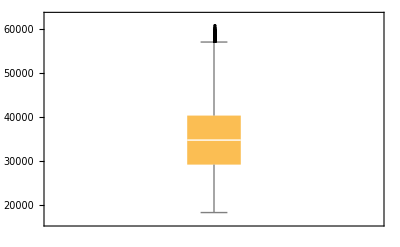

```mathematica
BoxWhiskerChart[demand09to23DS[All,"TSD_EMBEDDED"],"Outliers"]
```

205 outliers identified

```mathematica
Counts[(#>56992.5)&/@demand09to23DS[All,"TSD_EMBEDDED"]]
```

```mathematica
Query[GroupBy["SETTLEMENT_YEAR"],BoxWhiskerChart[#,"Outliers"]&, "TSD_EMBEDDED"][demand09to23DS]
```

## 3 Creating the half-hourly time series

### 3.1 Review number of periods per day

Check for summer/winter time change: in March, days with 46 periods, in October, days with 50 period.

```mathematica
SortBy[Tally[#["SETTLEMENT_DATE"]&/@(demand09to23DS//Normal)],Last]
```

To ensure a regularly sampled time series we manipulate the data so that every day has only 48 periods.
For the days with 46 periods, we input in period 47 and 48 the average of period 46 and period 1 of the next day.
For the days with 50 periods, we replace the value of period 48 with an average of period 48, 49 and 50.

### 3.2 Handle day with 50 periods

Convert period to time: each period is an increment of 30 minutes. There are 48 periods in 24 hours.
Periods 49 and 50 are allocated the same time as period 48 to allow easy detection.

```mathematica
periodTime[period_]:=(
Which[period==49,{23,45,0},
period==50,{23,45,0},
True,If[OddQ[period],{IntegerPart[period/2],15,00},{IntegerPart[period/2]-1,45,00}]]
)
```

```mathematica
timePeriod=DateObject[Join[DateList[#["SETTLEMENT_DATE"]][[1;;3]],periodTime[#["SETTLEMENT_PERIOD"]]],TimeZone->None]&/@(demand09to23DS//Normal);
```

```mathematica
SortBy[Tally[timePeriod],Last]
```

```mathematica
timePeriod//Dimensions
DeleteDuplicates[timePeriod]//Dimensions
```

{262944}

{262914}

Select demand data for each time period

```mathematica
tsdData=#["TSD_EMBEDDED"]&/@(demand09to23DS//Normal)
```

```mathematica
tsdData//Dimensions
```

{262944}

Days with 50 periods

```mathematica
date50=Flatten[Cases[Tally[#["SETTLEMENT_DATE"]&/@(demand09to23DS//Normal)],{_,50}][[All,1]]]
```

{Sun 25 Oct 2009,Sun 31 Oct 2010,Sun 30 Oct 2011,Sun 28 Oct 2012,Sun 27 Oct 2013,Sun 26 Oct 2014,Sun 25 Oct 2015,Sun 30 Oct 2016,Sun 29 Oct 2017,Sun 28 Oct 2018,Sun 27 Oct 2019,Sun 25 Oct 2020,Sun 31 Oct 2021,Sun 30 Oct 2022,Sun 29 Oct 2023}

Calculate average for period 48, 49 and 50. The average value will replace period 48 and period 49 and 50 will be deleted.

```mathematica
days=#["SETTLEMENT_DATE"]&/@(demand09to23DS//Normal);
```

```mathematica
position50=Flatten[(Position[days,#]&/@date50)[[All,{48,49,50}]]]
```

{14302,14303,14304,32110,32111,32112,49582,49583,49584,67054,67055,67056,84526,84527,84528,101998,101999,102000,119470,119471,119472,137278,137279,137280,154750,154751,154752,172222,172223,172224,189694,189695,189696,207166,207167,207168,224974,224975,224976,242446,242447,242448,259918,259919,259920}

Replace values for period 48.

```mathematica
avg50=Table[Mean[tsdData[[position50[[n;;n+2]]]]]//N,{n,1,Length[position50],3}]
```

{30870.,31139.3,30047.7,31810.3,29567.7,27760.,28772.,27049.3,27573.7,29273.,27891.,25900.,26542.3,26249.,26638.}

```mathematica
(tsdData[[position50[[1;;;;3]][[#]]]]=avg50[[#]])&/@Range[1,Length[avg50]]
```

{30870.,31139.3,30047.7,31810.3,29567.7,27760.,28772.,27049.3,27573.7,29273.,27891.,25900.,26542.3,26249.,26638.}

```mathematica
tsdData[[224974]]
```

26542.3

Delete periods 49 and 50.

```mathematica
Complement[position50,position50[[1;;;;3]]]//Reverse
```

{259920,259919,242448,242447,224976,224975,207168,207167,189696,189695,172224,172223,154752,154751,137280,137279,119472,119471,102000,101999,84528,84527,67056,67055,49584,49583,32112,32111,14304,14303}

```mathematica
tsdData2=Fold[Drop[#1,{#2}]&,tsdData,(Complement[position50,position50[[1;;;;3]]]//Reverse)]
```

```mathematica
tsdData2//Dimensions
```

{262914}

```mathematica
tsdData2[[14302]]
```

30870.

```mathematica
tsdData2[[259890]]
```

26638.

### 3.3 Handle days with 46 periods

Days with 46 periods

```mathematica
date46=Flatten[Cases[Tally[#["SETTLEMENT_DATE"]&/@(demand09to23DS//Normal)],{_,46}][[All,1]]]
```

{Sun 29 Mar 2009,Sun 28 Mar 2010,Sun 27 Mar 2011,Sun 25 Mar 2012,Sun 31 Mar 2013,Sun 30 Mar 2014,Sun 29 Mar 2015,Sun 27 Mar 2016,Sun 26 Mar 2017,Sun 25 Mar 2018,Sun 31 Mar 2019,Sun 29 Mar 2020,Sun 28 Mar 2021,Sun 27 Mar 2022,Sun 26 Mar 2023}

```mathematica
position46=Table[Flatten[(Position[days,#]&/@date46)[[All,-1]]][[i]]-2*(i-1),{i,1,15}]
```

{4222,21692,39162,56632,74438,91908,109378,126848,144318,161788,179594,197064,214534,232004,249474}

```mathematica
DeleteDuplicates[timePeriod][[#]]&/@position46
```

{Sun 29 Mar 2009 22:45:00,Sun 28 Mar 2010 22:45:00,Sun 27 Mar 2011 22:45:00,Sun 25 Mar 2012 22:45:00,Sun 31 Mar 2013 22:45:00,Sun 30 Mar 2014 22:45:00,Sun 29 Mar 2015 22:45:00,Sun 27 Mar 2016 22:45:00,Sun 26 Mar 2017 22:45:00,Sun 25 Mar 2018 22:45:00,Sun 31 Mar 2019 22:45:00,Sun 29 Mar 2020 22:45:00,Sun 28 Mar 2021 22:45:00,Sun 27 Mar 2022 22:45:00,Sun 26 Mar 2023 22:45:00}

Take the average of period 46 and period 1 of the next day.

```mathematica
avg46=N[Mean[{tsdData2[[#]],tsdData2[[#+1]]}]]&/@Reverse[position46]
```

{25550.,24387.5,27683.5,26227.5,26836.,28333.,26609.5,27424.,29239.5,28980.5,31767.5,29349.5,30440.5,30362.5,30739.5}

Insert values for period 47 and 48.

```mathematica
tsdData3=Insert[tsdData2,avg46[[1]],{{Reverse[position46][[1]]+1},{Reverse[position46][[1]]+1}}];
tsdData3=Insert[tsdData3,avg46[[2]],{{Reverse[position46][[2]]+1},{Reverse[position46][[2]]+1}}];
tsdData3=Insert[tsdData3,avg46[[3]],{{Reverse[position46][[3]]+1},{Reverse[position46][[3]]+1}}];
tsdData3=Insert[tsdData3,avg46[[4]],{{Reverse[position46][[4]]+1},{Reverse[position46][[4]]+1}}];
tsdData3=Insert[tsdData3,avg46[[5]],{{Reverse[position46][[5]]+1},{Reverse[position46][[5]]+1}}];
tsdData3=Insert[tsdData3,avg46[[6]],{{Reverse[position46][[6]]+1},{Reverse[position46][[6]]+1}}];
tsdData3=Insert[tsdData3,avg46[[7]],{{Reverse[position46][[7]]+1},{Reverse[position46][[7]]+1}}];
tsdData3=Insert[tsdData3,avg46[[8]],{{Reverse[position46][[8]]+1},{Reverse[position46][[8]]+1}}];
tsdData3=Insert[tsdData3,avg46[[9]],{{Reverse[position46][[9]]+1},{Reverse[position46][[9]]+1}}];
tsdData3=Insert[tsdData3,avg46[[10]],{{Reverse[position46][[10]]+1},{Reverse[position46][[10]]+1}}];
tsdData3=Insert[tsdData3,avg46[[11]],{{Reverse[position46][[11]]+1},{Reverse[position46][[11]]+1}}];
tsdData3=Insert[tsdData3,avg46[[12]],{{Reverse[position46][[12]]+1},{Reverse[position46][[12]]+1}}];
tsdData3=Insert[tsdData3,avg46[[13]],{{Reverse[position46][[13]]+1},{Reverse[position46][[13]]+1}}];
tsdData3=Insert[tsdData3,avg46[[14]],{{Reverse[position46][[14]]+1},{Reverse[position46][[14]]+1}}];
tsdData3=Insert[tsdData3,avg46[[15]],{{Reverse[position46][[15]]+1},{Reverse[position46][[15]]+1}}];
```

```mathematica
tsdData3//Dimensions
```

{262944}

```mathematica
tsdData3[[144334;;144339]]
```

{27039,26609.5,26609.5,26180,26254,26662}

```mathematica
newDates={DateObject[Join[DateList[Reverse[date46][[#]]][[1;;3]],{23,15,00}],TimeZone->None],
DateObject[Join[DateList[Reverse[date46][[#]]][[1;;3]],{23,45,00}],TimeZone->None]}&/@Range[15]
```

{{Sun 26 Mar 2023 23:15:00,Sun 26 Mar 2023 23:45:00},{Sun 27 Mar 2022 23:15:00,Sun 27 Mar 2022 23:45:00},{Sun 28 Mar 2021 23:15:00,Sun 28 Mar 2021 23:45:00},{Sun 29 Mar 2020 23:15:00,Sun 29 Mar 2020 23:45:00},{Sun 31 Mar 2019 23:15:00,Sun 31 Mar 2019 23:45:00},{Sun 25 Mar 2018 23:15:00,Sun 25 Mar 2018 23:45:00},{Sun 26 Mar 2017 23:15:00,Sun 26 Mar 2017 23:45:00},{Sun 27 Mar 2016 23:15:00,Sun 27 Mar 2016 23:45:00},{Sun 29 Mar 2015 23:15:00,Sun 29 Mar 2015 23:45:00},{Sun 30 Mar 2014 23:15:00,Sun 30 Mar 2014 23:45:00},{Sun 31 Mar 2013 23:15:00,Sun 31 Mar 2013 23:45:00},{Sun 25 Mar 2012 23:15:00,Sun 25 Mar 2012 23:45:00},{Sun 27 Mar 2011 23:15:00,Sun 27 Mar 2011 23:45:00},{Sun 28 Mar 2010 23:15:00,Sun 28 Mar 2010 23:45:00},{Sun 29 Mar 2009 23:15:00,Sun 29 Mar 2009 23:45:00}}

Insert dates for period 47 and 48

```mathematica
timePeriod2=Insert[DeleteDuplicates[timePeriod],newDates[[1]],{Reverse[position46][[1]]+1}]//Flatten;
```

```mathematica
timePeriod2=Insert[timePeriod2,newDates[[2]],{Reverse[position46][[2]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[3]],{Reverse[position46][[3]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[4]],{Reverse[position46][[4]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[5]],{Reverse[position46][[5]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[6]],{Reverse[position46][[6]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[7]],{Reverse[position46][[7]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[8]],{Reverse[position46][[8]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[9]],{Reverse[position46][[9]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[10]],{Reverse[position46][[10]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[11]],{Reverse[position46][[11]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[12]],{Reverse[position46][[12]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[13]],{Reverse[position46][[13]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[14]],{Reverse[position46][[14]]+1}]//Flatten;
timePeriod2=Insert[timePeriod2,newDates[[15]],{Reverse[position46][[15]]+1}]//Flatten;
```

```mathematica
timePeriod2//Dimensions
```

{262944}

```mathematica
timePeriod2[[144334;;144339]]
```

{Sun 26 Mar 2017 22:45:00,Sun 26 Mar 2017 23:15:00,Sun 26 Mar 2017 23:45:00,Mon 27 Mar 2017 00:15:00,Mon 27 Mar 2017 00:45:00,Mon 27 Mar 2017 01:15:00}

### 3.4 Putting the clean time series together

```mathematica
halfhourlyDemandTS=TimeSeries[Transpose[{timePeriod2,tsdData3}]]
```

TemporalData[TimeSeries, «1»]

```mathematica
Export["exp_half_hour_demand09to23.csv",halfhourlyDemandTS]
```

exp_half_hour_demand09to23.csv

```mathematica
halfhourlyDemand=Import["exp_half_hour_demand09to23.csv"];
```

```mathematica
halfhourlyDemandDS=Dataset[AssociationThread[hourlyDemand[[1]]->ToExpression[#]]&/@hourlyDemand[[2;;]]];
```

### 3.5 Stats summary

```mathematica
hourlyDemandDS=Dataset[AssociationThread[{"TIME","HOUR","TSD_EMBEDDED"}->#]&/@Transpose[{timePeriod2,DateObject[#,"Hour"]&/@timePeriod2,tsdData3}]];
```

```mathematica
statsSummary[hourlyDemandDS]
```

rows→262944
total#NA→0

Dataset[<>]

## 4 Creating time series on different timescales

Yearly total demand for TSD + Embedded generation
Monthly total demand for TSD + Embedded generation
Daily peak demand (max daily value) for TSD + Embedded generation
Daily total demand for TSD + Embedded generation

Hourly total demand for TSD + Embedded generation

Monthly total demand for TSD only
Monthly total demand for National Demand only

```mathematica
yearlyTotalDemand09to23=Query[GroupBy["SETTLEMENT_YEAR"],Total, "TSD_EMBEDDED"][demand09to23DS];
monthlyTotalDemand09to23=Query[GroupBy["SETTLEMENT_MONTH"], Total, "TSD_EMBEDDED"][demand09to23DS];
dailyPeakDemand09to23=Query[GroupBy["SETTLEMENT_DATE"], Max, "TSD_EMBEDDED"][demand09to23DS];
dailyTotalDemand09to23=Query[GroupBy["SETTLEMENT_DATE"], Total, "TSD_EMBEDDED"][demand09to23DS];
```

```mathematica
hourlyTotalDemand09to23=Query[GroupBy["HOUR"], Total, "TSD_EMBEDDED"][hourlyDemandDS];
```

```mathematica
monthlyTotalTSD09to23=Query[GroupBy["SETTLEMENT_MONTH"],Total, "TSD"][demand09to23DS];
monthlyTotalND09to23=Query[GroupBy["SETTLEMENT_MONTH"], Total, "ND"][demand09to23DS];
```

```mathematica
Export["exp_yearly_total_demand09to23.csv",yearlyTotalDemand09to23]
Export["exp_monthly_total_demand09to23.csv",monthlyTotalDemand09to23]
Export["exp_daily_peak_demand09to23.csv",dailyPeakDemand09to23]
Export["exp_daily_total_demand09to23.csv",dailyTotalDemand09to23]
```

exp_yearly_total_demand09to23.csv

exp_monthly_total_demand09to23.csv

exp_daily_peak_demand09to23.csv

exp_daily_total_demand09to23.csv

```mathematica
Export["exp_hourly_total_demand09to23.csv",hourlyTotalDemand09to23]
```

exp_hourly_total_demand09to23.csv

```mathematica
yearlyTotalDemand09to23TS=TimeSeries[yearlyTotalDemand09to23//Normal]
monthlyTotalDemand09to23TS=TimeSeries[monthlyTotalDemand09to23//Normal]
dailyPeakDemand09to23TS=TimeSeries[dailyPeakDemand09to23//Normal]
dailyTotalDemand09to23TS=TimeSeries[dailyTotalDemand09to23//Normal]
```

TimeSeries[…]

TimeSeries[…]

TimeSeries[…]

«1 more identical outputs»

```mathematica
hourlyTotalDemand09to23TS=TimeSeries[hourlyTotalDemand09to23//Normal]
```

TemporalData[TimeSeries, «1»]

```mathematica
monthlyTotalTSD09to23TS=TimeSeries[monthlyTotalTSD09to23//Normal]
monthlyTotalND09to23TS=TimeSeries[monthlyTotalND09to23//Normal]
```

TimeSeries[…]

TimeSeries[…]